1-a_2^2>0&&(-a_1-a_1 a_2) (a_1+a_1 a_2)+(1-a_2^2)^2>0

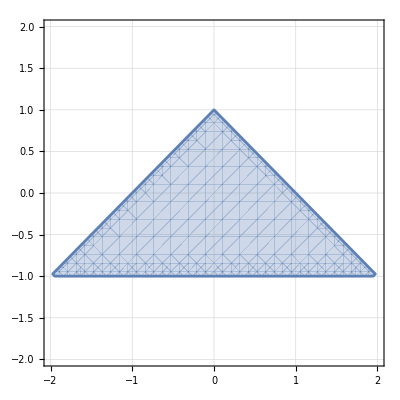

ARMAProcess[{-3/2,-3/4},{-1,-1},1]

1-b_2^2>0&&(b_1-b_1 b_2) (-b_1+b_1 b_2)+(1-b_2^2)^2>0

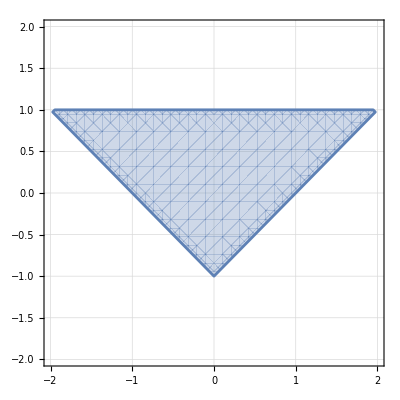

ARMAProcess[{-3/2,-3/4},{-3/2,5/8},1]

True

```mathematica
arma=ARMAProcess[{Subscript[a,1],Subscript[a,2]},{Subscript[b,1],Subscript[b,2]},σ];
ws=WeakStationarity[arma]
RegionPlot[ws,{Subscript[a,1],-2,2},{Subscript[a,2],-2,2},GridLines->Automatic]
aspt=ProcessParameterAssumptions[arma];
rest=Subscript[a,1]!=0&&Subscript[a,2]!=0&&Subscript[b,1]!=0&&Subscript[b,2]!=0&&σ!=0;
wsARMA=arma/. FindInstance[ws&&rest&&aspt,{Subscript[a,1],Subscript[a,2],Subscript[b,1],Subscript[b,2],σ}][[1]]
in=TimeSeriesInvertibility[arma]
RegionPlot[in,{Subscript[b,1],-2,2},{Subscript[b,2],-2,2},GridLines->Automatic]
aspt=ProcessParameterAssumptions[arma];
rest=Subscript[a,1]!=0&&Subscript[a,2]!=0&&Subscript[b,1]!=0&&Subscript[b,2]!=0&&σ!=0;
invARMA=arma/. FindInstance[in&&rest&&aspt,{Subscript[a,1],Subscript[a,2],Subscript[b,1],Subscript[b,2],σ}][[1]]
TimeSeriesInvertibility[invARMA]
```